```mathematica
Clear[H,A,B,x1,x0,psi,out,Dmat,d1,d2,d3,d4,psi0,U,Re0,Re1,Im1,Im0]
Clear[sigX,sigZ,sigY,theta1,theta2,theta3,alpha]
(* Section used for universal objects (pauli's, H, etc.) and functions. If new functions need to be written/tested use a new cell beneath and then merge. 
*)

sigX = PauliMatrix[1];
sigY = PauliMatrix[2];
sigZ = PauliMatrix[3];
H = 1/(Sqrt[2])*{{1,1},{1,-1}};

rz[theta_] = Cos[theta/2]*IdentityMatrix[2] - I*Sin[theta/2]*sigZ;
rx[theta_] =Cos[theta/2]*IdentityMatrix[2] - I*Sin[theta/2]*sigX;

prod[psi_,phi_]:=( psi.Conjugate[phi])*(phi.Conjugate[psi]);

buildU[alpha_,theta1_,theta2_,theta3_]:= Exp[I*alpha]*rx[theta1].rz[theta2].rx[theta3];
getArgMins[psi_,phi_,params_]:= Module[{Re0,Re1,Im0,Im1},
Re0 = Abs[Re[psi[[1]]] - Re[phi[[1]]]]^2;
Re1 = Abs[Re[psi[[2]]] - Re[phi[[2]]]]^2; 
Im0 = Abs[(Im[psi[[1]]] - Im[phi[[1]]])]^2; 
Im1 = Abs[(Im[psi[[2]]]-  Im[phi[[2]]])]^2;
Return[NArgMin[Re0+Re1+Im0+Im1,params]]
]
getAverageOverlap[alpha_,theta1_,theta2_,theta3_]:= Module[{A,B,psi,psi0,t,AtU,UtB,Dmat,d1,d2 ,d3,d4,finalMat,phi,temp,tot,U,n},
n = 10;
t = {0,0,0,0};
U = buildU[alpha,theta1,theta2,theta3];
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[U,B]];
Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4}];
t = t +temp  ;
(*Print[StringForm["Output temp: ``",temp]];*)
];
(*Print[StringForm["Average t: ``",t/n]];*)
t = t/Mean[Abs[t]];
(*Print[StringForm["Final t: ``",t]];*)
Dmat = DiagonalMatrix[t];
tot = 0;

For[i=0,i<n,i++,
(*Print[StringForm["Second For Loop:``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[U,B]];
finalMat = UtB.Dmat.AtU;
phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
tot =tot + prod[phi,psi];
];
(*Print[StringForm["Final Average Overlap: ``",tot/n]];*)
Return[Abs[tot/n]]
]

getAvgOverlapList[list_]:=getAverageOverlap[list[[1]],list[[2]],list[[3]],list[[4]]];
h[a_] := getAverageOverlap[Pi/2,a[[1]],a[[2]],Pi/2];
```

```mathematica
getOptDmat[U_,n_] := Module[{A,B,psi,psi0,t,AtU,UtB,Dmat,d1,d2 ,d3,d4,finalMat,phi,temp,tot},
t = {0,0,0,0};
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4}];
t = t +temp  ;
];

(* Line below converts a random t to unitary t. *)
t = t/Mean[Abs[t]];
Dmat = DiagonalMatrix[t];
Return[Dmat]
];

testOptMat[Dmat_,U_,n_]:=Module[{A,B,psi,psi0,AtU,UtB,finalMat,phi,results},
results = {};
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
AppendTo[results,prod[phi,psi]];
];
Return[results]
]
```

```mathematica
Module[{U,n,Dmat,results},
U = buildU[Pi/2,Pi/2,Pi/2,Pi/2];
n = 100;
Dmat = getOptDmat[U,n];
results=testOptMat[Dmat,U,n];
Print[Dmat];
Print[results];
]
```

{{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.999999,0.},{0.,0.,0.,-1.}}

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

Time Elapsed 1: 3.07446

Time Elapsed 2: 2.4183

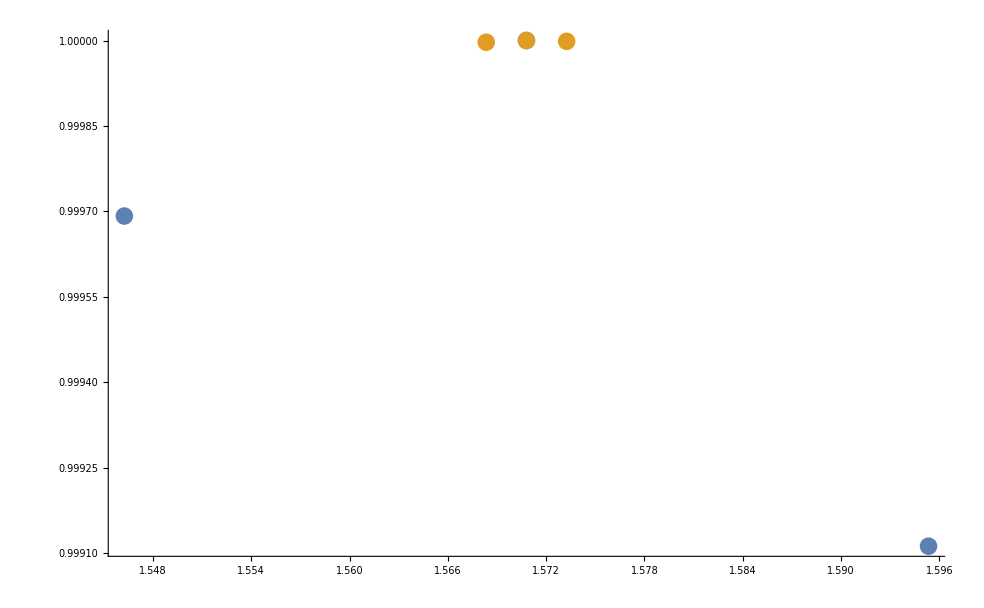

```mathematica
Clear[dx,dy,ay,by,ax,bx,xAxis,yAxis]
(* Code for Horizontal Section, getting profile of peak along significant axis. 
*)
dx = Pi/(64*2);
dy = dx/10;
ax = Pi/2 - 1*dx;
bx= Pi/2 + 1*dx;
ay = Pi/2 - 1*dy;
by = Pi/2 + 1*dy;

xAxis = AbsoluteTiming[Table[{i,h[{i,Pi/2}]},{i,ax,bx,dx}]];
yAxis = AbsoluteTiming[Table[{i,h[{i,Pi/2}]},{i,ay,by,dy}]];

Print[StringForm["Time Elapsed 1: ``",xAxis[[1]]]]
Print[StringForm["Time Elapsed 2: ``",yAxis[[1]]]]

xAxis = xAxis[[2]];
yAxis = yAxis[[2]];
ListPlot[{xAxis,yAxis}]
(*time = AbsoluteTiming[Map[h,xAxis]];
yAxis = time[[2]];
Print[StringForm["Time Elapsed: ``",time[[1]]]]
yAxis = Table[Append[xAxis[[i]],yAxis[[i]]],{i,1,Length[newTab]}]*)
```

```mathematica
tab0 =  Table[{i,j},{i,7Pi/16,9Pi/16,Pi/(64)},{j,3Pi/8,5Pi/8,Pi/16}]
tab0 = Flatten[tab0,1]
time = AbsoluteTiming[Map[h,tab0]];
Print[StringForm["Total Time elapsed: ``",time[[1]]]]
newTab = time[[2]];
Export["data.csv",newTab]
plotter = Table[Append[tab0[[i]],newTab[[i]]],{i,1,Length[newTab]}]
```

{{{(7 π)/16,(3 π)/8},{(7 π)/16,(7 π)/16},{(7 π)/16,π/2},{(7 π)/16,(9 π)/16},{(7 π)/16,(5 π)/8}},{{(29 π)/64,(3 π)/8},{(29 π)/64,(7 π)/16},{(29 π)/64,π/2},{(29 π)/64,(9 π)/16},{(29 π)/64,(5 π)/8}},{{(15 π)/32,(3 π)/8},{(15 π)/32,(7 π)/16},{(15 π)/32,π/2},{(15 π)/32,(9 π)/16},{(15 π)/32,(5 π)/8}},{{(31 π)/64,(3 π)/8},{(31 π)/64,(7 π)/16},{(31 π)/64,π/2},{(31 π)/64,(9 π)/16},{(31 π)/64,(5 π)/8}},{{π/2,(3 π)/8},{π/2,(7 π)/16},{π/2,π/2},{π/2,(9 π)/16},{π/2,(5 π)/8}},{{(33 π)/64,(3 π)/8},{(33 π)/64,(7 π)/16},{(33 π)/64,π/2},{(33 π)/64,(9 π)/16},{(33 π)/64,(5 π)/8}},{{(17 π)/32,(3 π)/8},{(17 π)/32,(7 π)/16},{(17 π)/32,π/2},{(17 π)/32,(9 π)/16},{(17 π)/32,(5 π)/8}},{{(35 π)/64,(3 π)/8},{(35 π)/64,(7 π)/16},{(35 π)/64,π/2},{(35 π)/64,(9 π)/16},{(35 π)/64,(5 π)/8}},{{(9 π)/16,(3 π)/8},{(9 π)/16,(7 π)/16},{(9 π)/16,π/2},{(9 π)/16,(9 π)/16},{(9 π)/16,(5 π)/8}}}

{{(7 π)/16,(3 π)/8},{(7 π)/16,(7 π)/16},{(7 π)/16,π/2},{(7 π)/16,(9 π)/16},{(7 π)/16,(5 π)/8},{(29 π)/64,(3 π)/8},{(29 π)/64,(7 π)/16},{(29 π)/64,π/2},{(29 π)/64,(9 π)/16},{(29 π)/64,(5 π)/8},{(15 π)/32,(3 π)/8},{(15 π)/32,(7 π)/16},{(15 π)/32,π/2},{(15 π)/32,(9 π)/16},{(15 π)/32,(5 π)/8},{(31 π)/64,(3 π)/8},{(31 π)/64,(7 π)/16},{(31 π)/64,π/2},{(31 π)/64,(9 π)/16},{(31 π)/64,(5 π)/8},{π/2,(3 π)/8},{π/2,(7 π)/16},{π/2,π/2},{π/2,(9 π)/16},{π/2,(5 π)/8},{(33 π)/64,(3 π)/8},{(33 π)/64,(7 π)/16},{(33 π)/64,π/2},{(33 π)/64,(9 π)/16},{(33 π)/64,(5 π)/8},{(17 π)/32,(3 π)/8},{(17 π)/32,(7 π)/16},{(17 π)/32,π/2},{(17 π)/32,(9 π)/16},{(17 π)/32,(5 π)/8},{(35 π)/64,(3 π)/8},{(35 π)/64,(7 π)/16},{(35 π)/64,π/2},{(35 π)/64,(9 π)/16},{(35 π)/64,(5 π)/8},{(9 π)/16,(3 π)/8},{(9 π)/16,(7 π)/16},{(9 π)/16,π/2},{(9 π)/16,(9 π)/16},{(9 π)/16,(5 π)/8}}

Total Time elapsed: 110.453

data.csv

{{(7 π)/16,(3 π)/8,0.994176},{(7 π)/16,(7 π)/16,0.581815},{(7 π)/16,π/2,0.455733},{(7 π)/16,(9 π)/16,0.343565},{(7 π)/16,(5 π)/8,0.468524},{(29 π)/64,(3 π)/8,0.378788},{(29 π)/64,(7 π)/16,0.989089},{(29 π)/64,π/2,0.528739},{(29 π)/64,(9 π)/16,0.665596},{(29 π)/64,(5 π)/8,0.436808},{(15 π)/32,(3 π)/8,0.991289},{(15 π)/32,(7 π)/16,0.481484},{(15 π)/32,π/2,0.521128},{(15 π)/32,(9 π)/16,0.9967},{(15 π)/32,(5 π)/8,0.535146},{(31 π)/64,(3 π)/8,0.635796},{(31 π)/64,(7 π)/16,0.994971},{(31 π)/64,π/2,0.498956},{(31 π)/64,(9 π)/16,0.436945},{(31 π)/64,(5 π)/8,0.99957},{π/2,(3 π)/8,1.},{π/2,(7 π)/16,1.},{π/2,π/2,1.},{π/2,(9 π)/16,1.},{π/2,(5 π)/8,1.},{(33 π)/64,(3 π)/8,0.998907},{(33 π)/64,(7 π)/16,0.528187},{(33 π)/64,π/2,0.584051},{(33 π)/64,(9 π)/16,0.998453},{(33 π)/64,(5 π)/8,0.983858},{(17 π)/32,(3 π)/8,0.997085},{(17 π)/32,(7 π)/16,0.328812},{(17 π)/32,π/2,0.669747},{(17 π)/32,(9 π)/16,0.991953},{(17 π)/32,(5 π)/8,0.990326},{(35 π)/64,(3 π)/8,0.996652},{(35 π)/64,(7 π)/16,0.991177},{(35 π)/64,π/2,0.996011},{(35 π)/64,(9 π)/16,0.56667},{(35 π)/64,(5 π)/8,0.418337},{(9 π)/16,(3 π)/8,0.412932},{(9 π)/16,(7 π)/16,0.983173},{(9 π)/16,π/2,0.979299},{(9 π)/16,(9 π)/16,0.571411},{(9 π)/16,(5 π)/8,0.547783}}

plotter.csv

7.85398

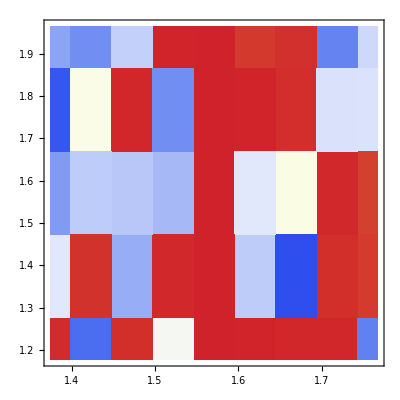

-Graphics3D-

```mathematica
ListDensityPlot[plotter,InterpolationOrder->0,ColorFunction->"TemperatureMap"]
ListPlot3D[plotter]
```

```mathematica
{{1,0},{0,-1}}.{{0,1},{1,0}}
```

{{0,1},{-1,0}}

```mathematica
Clear[alpha,theta1,theta2,theta3,AtU,UtB,Dmat,A,B,a1,a2,b1,b2,psi,psi0,psi1,Dmat,d1,d2,d3,d4]
(* This is Section used for analytic purposes. Idea is to use mathematica to simplify calculations and perform annoying tensor products and matrix calculations symbolically. 
*)
alpha = Pi/2;
theta3 = Pi/2;
U = buildU[alpha,theta1,theta2,theta3]//Simplify;

psi = {psi0,0,psi1,0};

A  = DiagonalMatrix[{a1,a2}];
B = DiagonalMatrix[{b1,b2}];

AtU= ArrayFlatten[TensorProduct[A,U]];
UtB =ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU.psi//Simplify;

Print["phi"]
phi = FullSimplify[finalMat[[1;;2]],{Element[theta1,Reals],Element[theta2,Reals]}]
Print["psi"]
psi = B.H.A.{psi0,psi1}//Simplify
```

phi

{1/2 b1 (a1 d1 psi0 (1+Cos[theta2])+a2 d3 psi1 (ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2]),1/2 (-a2 b2 d4 psi1 (-1+Cos[theta2])+a1 b2 d2 psi0 (-ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2])}

psi

{(b1 (a1 psi0+a2 psi1))/(√2),(b2 (a1 psi0-a2 psi1))/(√2)}